```mathematica
d=0.01;m=2500;l=6;K=1000; μ=1.3;λ=0.02;g=9.8;
theta=NDSolve[{θ''[t]==-d θ'[t]-(6K/m)θ[t]+f[t],θ[0]==0.01,θ'[0]==0.2},θ,{t,0,100}]
height=NDSolve[{y''[t]==-d y'[t]-(2K/m)y[t]+g,y'[0]==0.01,y[0]==0.01},y,{t,0,100}]
```

NDSolve::underdet: There are more dependent variables, {f[t],θ[t]}, than equations, so the system is underdetermined.

NDSolve[{θ''[t]==f[t]-(12 θ[t])/5-0.01 θ'[t],θ[0]==0.01,θ'[0]==0.2},θ,{t,0,100}]

{{y→InterpolatingFunction[…]}}

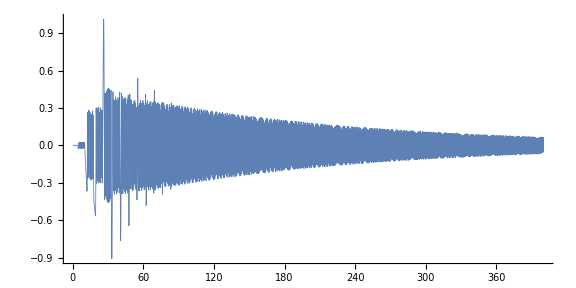

```mathematica
res=NDSolve[{θ''[t]==-d θ'[t]+3(K/m l)Cos[θ[t]](Max[y[t]-l Sin[θ[t]],0]    -  Max[y[t]+l Sin[θ[t]],0] )+λ Sin[μ t],
y''[t]==- d y'[t]-(K/m) (Max[y[t]-l Sin[θ[t]],0]    +  Max[y[t]+l Sin[θ[t]],0] )+g,y[0]==30,y'[0]==0,θ[0]==0.001,θ'[0]==0},{θ[t],y[t]},{t,0,1000},PrecisionGoal->40];
Plot[θ[t]/.res,{t,0,400},PlotRange->All,AspectRatio->1/2,ImageSize->Large,PlotStyle->Directive[Thickness[0.001]]]
```

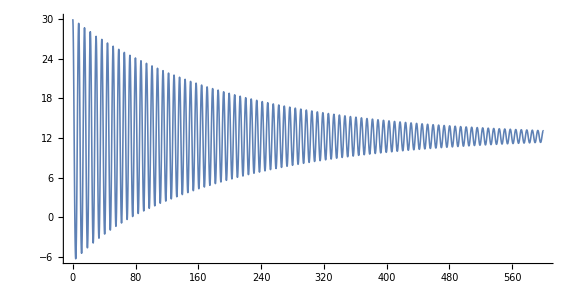

```mathematica
Plot[y[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/2,ImageSize->Large,PlotStyle->Directive[Thickness[0.002]]]
```

```mathematica
h=0.1;
pics=Table[Graphics[Rotate[Rectangle[{-2,-0.1},{2,0.1}],First[(θ[t]/.res)]],PlotRange->{{-5,5},{-5,5}},ImageSize->Large],{t,20,40,0.033}];
```

```mathematica
Export["simulationmckenna.mov",pics,"FrameRate"->30,ImageSize->Large]
```

simulationmckenna.mov

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["simulationmckenna.mov"]]]
```

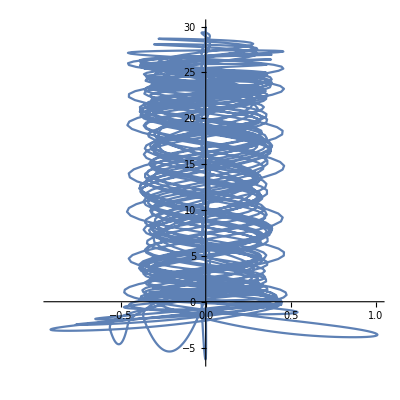

```mathematica
ParametricPlot[{First[θ[t]/.res],First[y[t]/.res]},{t,0,10},AspectRatio->1]
```

```mathematica
m=1000;c=0.01; k=1000; U=18;f=1;k0=2;c0=0.0001;
DSolve[{m x''[t]+(c-c0 U) x'[t]+(k-k0 U) x[t]== f U,x[0]==0,x'[0]==0},x[t],t ]
```

{{x[t]→0.0186722 ⅇ^(-4.1×10^-6 t) (1. ⅇ^(4.1×10^-6 t)-1. Cos[0.981835 t]-4.17585×10^-6 Sin[0.981835 t])}}

```mathematica
Solve[D[0.01867219917012448+ⅇ^(1/2 (-9.999999999999999*^-6+0.018 c0-√(-3.8559999999-3.5999999999786203*^-7 c0+0.00032399999999999996 c0^2)) t),t]==0,t]
```

{}

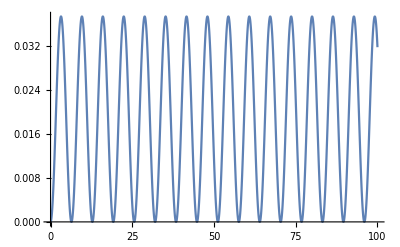

```mathematica
Plot[0.01867219917012448 ⅇ^(-4.1*^-6 t) (1. ⅇ^(4.1*^-6 t)-1. Cos[0.9818350166821257 t]-4.1758543241358*^-6 Sin[0.9818350166821257 t]),{t,0,100}]
```